```mathematica
Get[FileNameJoin[{NotebookDirectory[],"bouyancy.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"visualizations.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"COM.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Stability.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"boats.m"}]]
```

```mathematica
avs[boat_,front_,guess_]:=Module[{},
θ/.FindRoot[rightingArm[boat,front,θ],{θ,guess},AccuracyGoal->3,PrecisionGoal->Infinity (*only accuracy used*)]
]
```

```mathematica
ClearAll[rightingArm]
```

```mathematica
nPoints=50000
```

50000

```mathematica
boatWaterline[boat,{0,0,1}]
```

111.769

1.05206

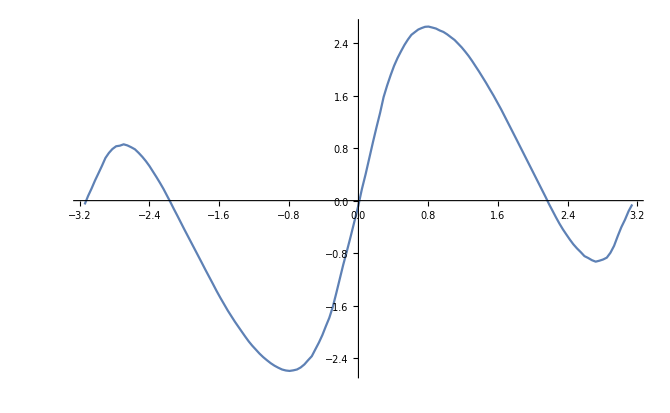

```mathematica
Plot[rightingArm[boat,{0,1,0},θ],{θ,-Pi,Pi},PlotPoints->20, MaxRecursion->3]
```

```mathematica
avs[boat,{0,1,0},Pi/2]
```

{θ→2.16741}

```mathematica
showBoat[boat,{0,0,1}]
```

-Graphics3D-